{{s→InterpolatingFunction[…],i→InterpolatingFunction[…],r→InterpolatingFunction[…],g→InterpolatingFunction[…]}}

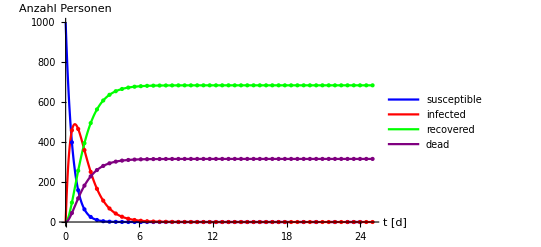

susceptile

{-5.23191×10^-12}

infected

{1.00528×10^-7}

recovered

{684.895}

dead

{316.105}

```mathematica
n=1000; (*Start Population*)
endt=25; (*Ende t der Simulation*)
b=1.8;(*Infektionsrate*)
k=0.65;(*Genesungsrate*)
u=0.3;(*Todesrate*)


system={
differenzialS=s'[t]==-b*s[t],(*Susceptile*)
differenzialI=i'[t]==b*s[t]-k*i[t]-u*i[t],(*Infective*)
differenzialR=r'[t]==k*i[t],(*Recovered*)
differenzialD=g'[t]==u*i[t]

};
anfangswerte={
s[0]==n,
i[0]==1,
r[0]==0,
g[0]==0
};
lösung=NDSolve[{system,anfangswerte},{s,i,r,g},{t,0,100}](*löse das GLS*)
lösungS=First[s/.lösung];(*erhalte erstes Element von Liste*)
lösungI=First[i/.lösung];
lösungR=First[r/.lösung];
lösungG=First[g/.lösung];


graph=
Plot[{lösungS[t],lösungI[t],lösungR[t],lösungG[t]},{t,0,endt},
PlotRange->{0,n},
PlotStyle->{Blue,Red,Green,Purple},
PlotLegends->{"susceptible","infected","recovered","dead"},
Mesh->Full,
AxesLabel->{"t [d]","Anzahl Personen"}
]
"susceptile"
s[endt]/.lösung
"infected"
i[endt]/.lösung
"recovered"
r[endt]/.lösung
"dead"
g[endt]/.lösung
```

```mathematica
{{□}, {□}}
```

{{□},{□}}